Articles for comparison:
R&I: https://arxiv.org/pdf/1202.2841.pdf
Dolgov et. al: https://arxiv.org/pdf/hep-ph/9703315.pdf
Mangano et. al: https://arxiv.org/pdf/hep-ph/0506164.pdf

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/standard_model_bbn

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = Map[Read[StringToStream[#],Number]&, linesEl, {2}];
```

```mathematica
T= Last[linesEl][[2]];
distEl1=Last[linesEl][[3;;]];
yEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesEl[[1]]][[4;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

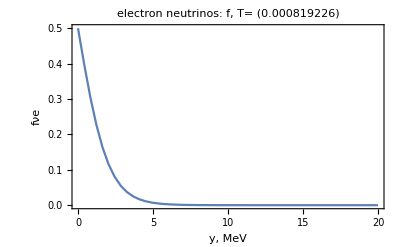

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electron neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνe"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ = Map[Read[StringToStream[#],Number]&, linesμ, {2}];
```

```mathematica
Last[linesμ][[3;;]]
```

{0.5,0.399245,0.306476,0.227145,0.163522,0.115076,0.0796218,0.0544227,0.0368814,0.0248468,0.0166722,0.0111568,0.0074526,0.00497229,0.00331485,0.00220879,0.0014713,0.000979848,0.000652482,0.000434462,0.000289279,0.00019261,0.000128248,0.000085395,0.0000568627,0.0000378645,0.0000252146,0.0000167916,0.0000111829,7.4479×10^-6,4.96061×10^-6,3.30412×10^-6,2.20086×10^-6,1.46606×10^-6,9.76626×10^-7,6.50629×10^-7,4.3347×10^-7,2.88808×10^-7,1.92436×10^-7,1.28226×10^-7,8.54477×10^-8,5.69417×10^-8,3.79479×10^-8,2.52904×10^-8,1.68548×10^-8,1.12333×10^-8,7.48633×10^-9,4.98882×10^-9,3.32412×10^-9,2.21449×10^-9}

```mathematica
Tμ= Last[linesμ][[2]];
distμ=Last[linesμ][[3;;]];
yμ=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesμ[[1]]][[4;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

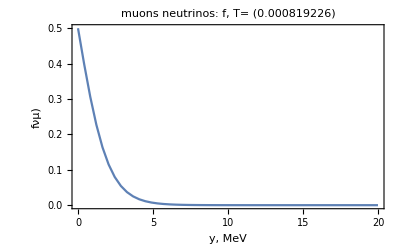

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνμ)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results (Fig. 10)

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
plotfEl=Interpolation[multiplier/@plotDataEl];
plotfμ=Interpolation[multiplier/@plotDataμ];
```

```mathematica
finalspectraSMTest=Import["../../figures/Figures-sources/Final-spectra-SM/spectra-test-SM.dat","HeaderLines"->3];
```

```mathematica
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-noosc.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-noosc.tsv"];
```

```mathematica
finalnueSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,4}]]];
finalnumuSMTestFunc=Interpolation[multiplier/@finalspectraSMTest[[All,{1,8}]]];
```

```mathematica
finalspectranueSMDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
```

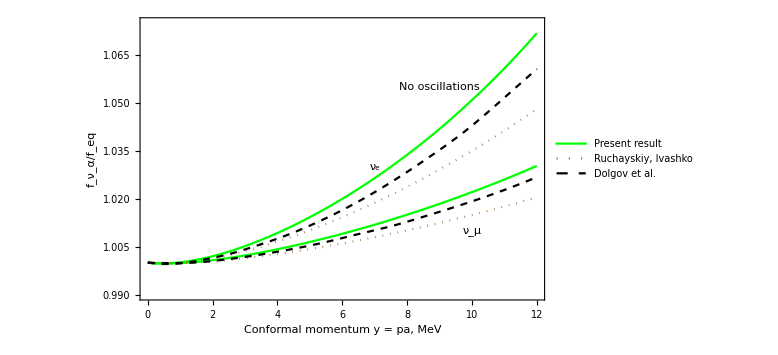

```mathematica
plt=Show[Plot[{
plotfEl[y],
plotfμ[y],
finalnueSMTestFunc[y],
finalnumuSMTestFunc[y],
finalspectranueSMDigitFunc[y],
finalspectranumuSMDigitFunc[y]
},{y,0,12},PlotRange->{{0,12},{0.99,1.075}},Frame->True,FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown,Dotted},{Brown,Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.03}],Text["ν_μ",{10,1.01}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Dolgov et al.",None},ImageSize->Large]]
Export["final-spectra-SM.png",%];
```

### Mangano, Dolgov, Ruchaiskyi

```mathematica
ManganoNuEl=finalspectranueSMDigitFunc;
```

```mathematica
DolgovNuElBoltzmann=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovBoltzmann.csv"];
```

```mathematica
DolgovNuElFermi=Import["../../figures/Figures-sources/Final-spectra-SM/DolgovVSMangano/DolgovFermi-Dirac.csv"];
```

```mathematica
DolgovNuElBoltzmannFunc=Interpolation[DolgovNuElBoltzmann];
DolgovNuElFermiFunc=Interpolation[DolgovNuElFermi];
```

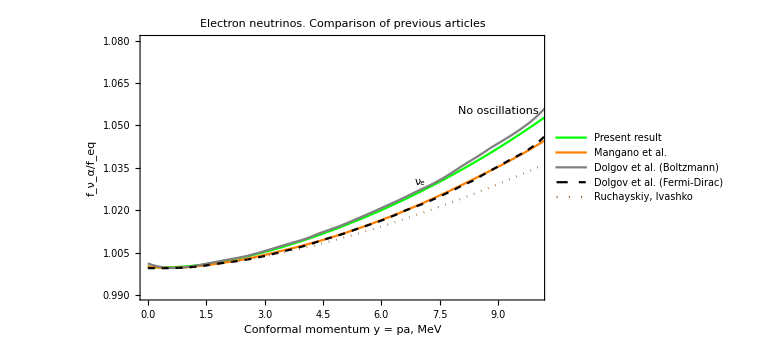

```mathematica
Show[Plot[{plotfEl[y],
ManganoNuEl[y],
DolgovNuElBoltzmannFunc[y]+1, DolgovNuElFermiFunc[y]+1, finalnueSMTestFunc[y]
},{y,0,12},PlotRange->{{0,10},{0.99,1.08}},Frame->True,PlotLabel-> "Electron neutrinos. Comparison of previous articles",FrameLabel->{"Conformal momentum y = pa, MeV","f_ν_α/f_eq"},PlotStyle->{{Green, Thick},{Orange, Thick},{Gray, Thick},{Black, Dashed}, {Brown,Dotted}},Epilog->{Text["ν_e",{7,1.03}],Text["No oscillations",{9,1.055}]},
PlotLegends->{"Present result","Mangano et al.","Dolgov et al. (Boltzmann)","Dolgov et al. (Fermi-Dirac)","Ruchayskiy, Ivashko"},ImageSize->Large]]
```

```mathematica
Export["Full-Comparison.png",%]
```

Full-Comparison.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Full-Comparison.png"]]]
```

## Final spectrum. Comparison with previous results (Fig. 11 of R&I article)

### Electron neutrinos

```mathematica
aEllist=First[Transpose[linesEl]];
```

```mathematica
setofdistributionsEl=Transpose[Transpose[linesEl][[3 ;;]]];
```

```mathematica
setofdistributionsEl1=Transpose[{yEl,#}]&/@setofdistributionsEl;
```

```mathematica
interpolatedDistEl=Interpolation/@setofdistributionsEl1;
```

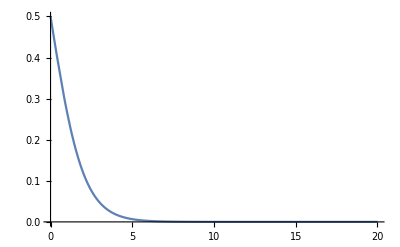

```mathematica
Plot[interpolatedDistEl[[20]][x],{x,0,20},PlotRange->All]
```

```mathematica
f3El=Interpolation[Transpose[{aEllist,#[3]&/@interpolatedDistEl}]];
f5El=Interpolation[Transpose[{aEllist,#[5]&/@interpolatedDistEl}]];
f7El=Interpolation[Transpose[{aEllist,#[7]&/@interpolatedDistEl}]];
```

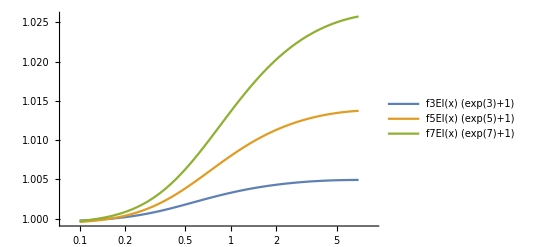

```mathematica
LogLinearPlot[{f3El[x]*(Exp[3]+1),f5El[x]*(Exp[5]+1),f7El[x]*(Exp[7]+1)},{x,0.1,7},PlotLegends->"Expressions"]
```

```mathematica
f3El[0.1]*(Exp[3]+1)-1
f5El[0.1]*(Exp[5]+1)-1
f7El[0.1]*(Exp[7]+1)-1
```

-0.000228661

-0.000404583

-0.000283742

```mathematica
(*sm-deltafnue_comp.eps*)
deltafnueTest=Import["../../figures/Figures-sources/sm-deltafnue_comp/semi_sm_upd_x.dat","HeaderLines"->2];
deltafnue3TestFunc=Interpolation[deltafnueTest[[All,{1,13}]]];
deltafnue5TestFunc=Interpolation[deltafnueTest[[All,{1,14}]]];
deltafnue7TestFunc=Interpolation[deltafnueTest[[All,{1,15}]]];
```

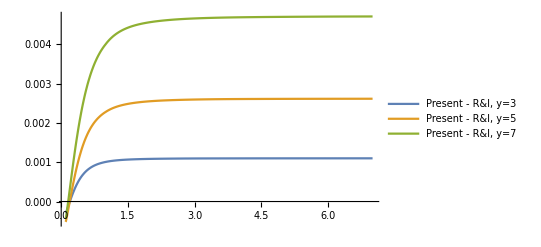

```mathematica
Show[Plot[{(f3El[x]-deltafnue3TestFunc[x])*(Exp[3]+1),(f5El[x]-deltafnue5TestFunc[x])*(Exp[5]+1),(f7El[x]-deltafnue7TestFunc[x])*(Exp[7]+1)},{x,0.1,7},PlotLegends->{"Present - R&I, y=3","Present - R&I, y=5","Present - R&I, y=7"}]]
```

```mathematica
deltafnue3Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue3-semi.dat","HeaderLines"->1];
deltafnue5Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue5-semi.dat","HeaderLines"->1];
deltafnue7Digit=Import["../../figures/Figures-sources/sm-deltafnue_comp/sm-dfnue7-semi.dat","HeaderLines"->1];

deltafnue3DigitFunc=Interpolation[deltafnue3Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue5DigitFunc=Interpolation[deltafnue5Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
deltafnue7DigitFunc=Interpolation[deltafnue7Digit[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
f7El[0.1]*(Exp[7]+1)-1
```

-0.000283742

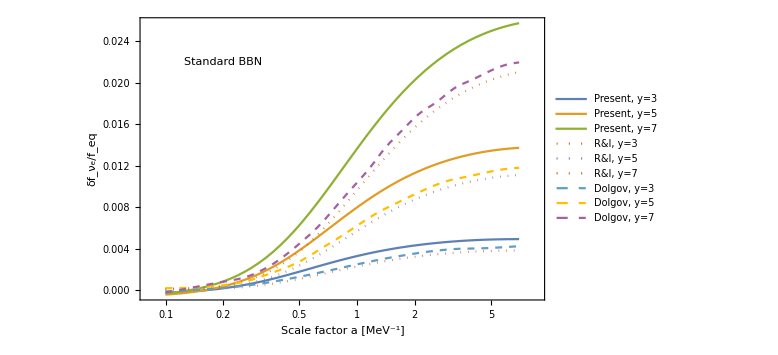

```mathematica
LogLinearPlot[{f3El[x]*(Exp[3]+1)-1,f5El[x]*(Exp[5]+1)-1,f7El[x]*(Exp[7]+1)-1,deltafnue3TestFunc[x]*(Exp[3]+1)-1,deltafnue5TestFunc[x]*(Exp[5]+1)-1,deltafnue7TestFunc[x]*(Exp[7]+1)-1,deltafnue3DigitFunc[x],deltafnue5DigitFunc[x],deltafnue7DigitFunc[x]},{x,0.1,7},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν_e/f_eq"},PlotStyle->{{},{},{},{Dotted},{Dotted},{Dotted},{Dashed},{Dashed},{Dashed}},Epilog->{Text["Standard BBN",{Log[0.2],0.022}]},ImageSize->Large,PlotLegends->{"Present, y=3","Present, y=5","Present, y=7","R&I, y=3","R&I, y=5","R&I, y=7","Dolgov, y=3","Dolgov, y=5","Dolgov, y=7"}]
```

```mathematica
Export["final-spectra-SM-357-old.png",%]
```

final-spectra-SM-357-old.png

```mathematica
f10El=Interpolation[Transpose[{aEllist,#[10]&/@interpolatedDistEl}]];
```

```mathematica
f10El[0.1]*(Exp[10]+1)
```

0.999334

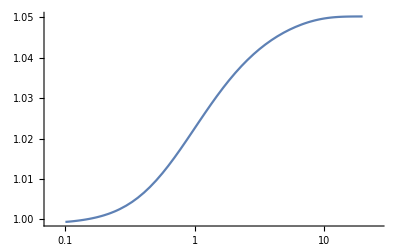

```mathematica
LogLinearPlot[f10El[x]*(Exp[10]+1),{x,0.1,20},Ticks -> Automatic]
```

## Convergence of the collision integral (draft)

```mathematica
rawlinesCollEl = Import["./output/Electron_neutrino.collision_integrals.txt", {"Text", "Lines"}][[2;; ]];
```

{##     0.000000e+00	4.081633e-01	8.163265e-01	1.224490e+00	1.632653e+00	2.040816e+00	2.448980e+00	2.857143e+00	3.265306e+00	3.673469e+00	4.081633e+00	4.489796e+00	4.897959e+00	5.306122e+00	5.714286e+00	6.122449e+00	6.530612e+00	6.938776e+00	7.346939e+00	7.755102e+00	8.163265e+00	8.571429e+00	8.979592e+00	9.387755e+00	9.795918e+00	1.020408e+01	1.061224e+01	1.102041e+01	1.142857e+01	1.183673e+01	1.224490e+01	1.265306e+01	1.306122e+01	1.346939e+01	1.387755e+01	1.428571e+01	1.469388e+01	1.510204e+01	1.551020e+01	1.591837e+01	1.632653e+01	1.673469e+01	1.714286e+01	1.755102e+01	1.795918e+01	1.836735e+01	1.877551e+01	1.918367e+01	1.959184e+01	2.000000e+01,3127,0.000000000000000000e+00	-0.000000000000000000e+00	-0.0000000000000000…00000000000000e+00	-0.000000000000000000e+00	-0.000000000000000000e+00}
 |  |  |  |

```mathematica
linesCollEl = Rest[StringSplit/@rawlinesCollEl[[3;; ;; 10]]];
```

```mathematica
linesCollEl[[1]]
```

{0.000000000000000000e+00,-7.907031847054213358e-06,1.788037824468347026e-06,9.094038082579913862e-06,1.302895061172648639e-05,1.412690034729990884e-05,1.335281410774769029e-05,1.161498994539655882e-05,9.560488594129168405e-06,7.571744202738983631e-06,5.833893558238045784e-06,4.402475105580450077e-06,3.271127136383888967e-06,2.400890309617320639e-06,1.745125368102229402e-06,1.258619075628075734e-06,9.017679118705768104e-07,6.425503278062461021e-07,4.557303962329783964e-07,3.219256611633469767e-07,2.265864080738810848e-07,1.589842676518599118e-07,1.112430752115561861e-07,7.764445047846180170e-08,5.407071399779125875e-08,3.757575981920210917e-08,2.606355558026213215e-08,1.804743646085897602e-08,1.247707509847376800e-08,8.613330095008382009e-09,5.938019319144411529e-09,4.088471297760765469e-09,2.811643688460955734e-09,1.931453620426641128e-09,1.325397802916087643e-09,9.086558118616156615e-10,6.223633438068190780e-10,4.259107403747680511e-10,2.912305844006142334e-10,1.989793132846817865e-10,1.358529947277937870e-10,9.268359193588697801e-11,6.319033798890300209e-11,4.305391197666017390e-11,2.931368646888246588e-11,1.994754500560439836e-11,1.356459665558917404e-11,9.217925709049972676e-12,6.260030025144498061e-12,4.247973196070082229e-12}

```mathematica
ICollEl = Map[Read[StringToStream[#],Number]&, linesCollEl, {2}];
```

```mathematica
yCollEl=Map[Read[StringToStream[#],Number]&,StringSplit[rawlinesCollEl[[1]]][[2;;]]];
```

```mathematica
Tlist=Select[Transpose[linesEl][[2]],#≤7&];
```

```mathematica
Length[Tlist]-Length[Max/@(Abs/@ICollEl)]
```

-11

```mathematica
Max/@(Abs/@ICollEl)
```

{0.0000141269003472999088,0.0000206043680961442988,0.0000248707526218083785,0.0000279560717331150954,0.0000303628167497294044,0.0000324547892738280552,0.0000344229322735145615,0.0000363624922172789411,0.0000383196045827816079,0.000040315845621918811,0.0000423604357813189836,0.0000444561600509985055,0.0000466022301814916773,0.0000487956740347073037,0.000051032022039265712,0.0000533056402041154342,0.0000556099193271819558,0.0000579373761233625828,0.0000602797072346561436,0.0000626278850113237695,0.00006524167119437152,0.0000679183951257655849,0.000070612900282540636,0.0000733157883825441559,0.0000760170730096376701,0.000078706213595403085,0.0000813722138870431877,0.0000840036874993899119,0.0000865889184531454248,0.0000891160754568076641,0.0000915732031625537957,0.0000939484533102330488,0.0000962301664308995441,0.0000984069056775283002,0.000100467725778763395,0.00010240224681989929,0.000104200855766123368,0.000105854710237274219,0.000107355753664606368,0.000108697038991856232,0.000109872613278660936,0.000110936757446999934,0.000112429161238658537,0.000113763190152660343,0.000114933701969022195,0.000115936938551719493,0.000116769985734066495,0.000117430928892048314,0.000117919182112125043,0.000118235665786947663,0.000118381717850724044,0.000118359648451082933,0.000118173497085649615,0.000117827614483090315,0.000117327611843798252,0.000116678974753092746,0.00011588889159863669,0.000114964311372922623,0.000113914085146937793,0.000112745246090284468,0.00011146551655905057,0.000110084674878052624,0.000108611472255937258,0.000107053693740866152,0.000105418561058279181,0.000103736228269646347,0.000102300371287444847,0.000100790448556153933,0.0000992154877255124745,0.0000975825642579586372,0.0000958992267863223447,0.0000941688675104579431,0.0000923998564750228013,0.0000906015719404074105,0.0000887763357426685218,0.000086916658317282014,0.0000850370895411067806,0.000083156879147061602,0.0000812711386810605063,0.000079379458428618932,0.0000774853109475337476,0.0000755871349267245307,0.0000736900101094839499,0.0000717912512637752798,0.0000699061442688275747,0.0000680436786204552391,0.0000662007792207042201,0.0000643749664708259672,0.0000625635132212032374,0.0000607667781626908266,0.0000589987416277359955,0.0000572568137768847407,0.0000555356124265493634,0.0000538391991922182456,0.000052168302990818205,0.0000505230779301868438,0.0000488840652490551975,0.0000472451351218872162,0.0000456866961795476811,0.0000441605363410424445,0.0000426412926168850959,0.0000411025141988652365,0.0000396800507318495477,0.0000382799975162662065,0.0000368469059397469323,0.0000353950127496283073,0.0000340032631696018939,0.0000326144350482060474,0.0000312016814696391975,0.0000297442081542698133,0.0000283997537131597255,0.0000270784884026653572,0.0000256973138768046283,0.0000243504197716681858,0.0000231569010389343077,0.0000218720196287769397,0.0000207572513977183348,0.0000195873020047976354,0.0000184183516527269831,0.0000172226900074790024,0.0000162020019489617084,0.0000150062834092246078,0.0000139187068493029642,0.0000128747613570290298,0.0000118789919789641374,0.0000109121620850416434,0.0000100549540282823813,9.16316129639938026×10^-6,8.53457548188885085×10^-6,8.07897599486295803×10^-6,7.5770849239376048×10^-6,7.05835370595764289×10^-6,6.52779925225388524×10^-6,6.0001678292564975×10^-6,5.48072946138233874×10^-6,4.98275012361659719×10^-6,4.50466812296212993×10^-6,4.05549542392691365×10^-6,3.63610637599265374×10^-6,3.27996461102486592×10^-6,2.966382863789363×10^-6,2.66565938211726916×10^-6,2.38148319731124047×10^-6,2.11732749555437749×10^-6,1.87355450265158652×10^-6,1.65033678278803109×10^-6,1.44743902197319585×10^-6,1.26419705814839745×10^-6,1.09949797710839903×10^-6,9.52175147617140283×10^-7,8.21106205250998755×10^-7,7.05010858581545108×10^-7,6.02542211680656692×10^-7,5.12615008219086121×10^-7,4.34044213903916898×10^-7,3.65613495034722291×10^-7,3.06344487555065825×10^-7,2.55365799617379707×10^-7,2.1168894193124288×10^-7,1.74432477351160742×10^-7,1.42911957823343982×10^-7,1.1641589914290762×10^-7,9.42587696783903084×10^-8,7.5830550727573609×10^-8,6.06712990958158116×10^-8,4.82658535361224494×10^-8,3.81816089856101826×10^-8,3.00452018819896694×10^-8,2.35516584012884778×10^-8,1.84002502123803424×10^-8,1.43384593087603207×10^-8,1.11599085528268915×10^-8,8.69891714216919354×10^-9,6.93745505486731418×10^-9,5.64571500660804304×10^-9,4.63984406451345421×10^-9,3.86993548318059766×10^-9,3.38216565864968288×10^-9,2.97982083452552615×10^-9,2.64387622905815078×10^-9,2.35910846413389663×10^-9,2.11484163514796819×10^-9,1.90297555491270032×10^-9,1.71755942801610217×10^-9,1.5539391995389451×10^-9,1.40843781082367059×10^-9,1.27821309092723823×10^-9,1.16118670234754973×10^-9,1.05561781538199284×10^-9,9.60103108127441374×10^-10,8.73559002911861171×10^-10,7.95026267041976098×10^-10,7.23634485666480032×10^-10,6.58744170323188882×10^-10,5.99715832549918559×10^-10,5.45981038158060983×10^-10,4.97131225074554095×10^-10,4.52615722679183818×10^-10,4.12114786740858108×10^-10,3.75255382323302911×10^-10,3.41628947353456169×10^-10,3.11075609715771861×10^-10,2.83222334473975934×10^-10,2.57891485944128362×10^-10,2.34781083463531104×10^-10,2.13820072758608148×10^-10,1.94670946029873448×10^-10,1.77227121866962989×10^-10,1.61382018859512755×10^-10,1.46940237755188718×10^-10,1.33777433575232863×10^-10,1.21804788477675174×10^-10,1.10897957483757636×10^-10,1.00985886319904239×10^-10,9.19619935757509666×10^-11,8.37374614093278069×10^-11,7.62412355470587499×10^-11,6.94022617153677856×10^-11,6.32027763458609115×10^-11,5.75361980281741125×10^-11,5.23669996255193837×10^-11,4.76774175695027225×10^-11,4.34319247233361239×10^-11,3.95594668134435778×10^-11,3.60067531346430769×10^-11,3.27560201185406186×10^-11,2.98427949019242078×10^-11,2.71782596428238321×10^-11,2.47624143412394915×10^-11,2.25242047235951759×10^-11,2.04991579266788904×10^-11,1.86872739504906349×10^-11,1.70174985214543995×10^-11,1.54720680711761816×10^-11,1.40865097364439862×10^-11,1.28252963804698084×10^-11,1.16706644348596455×10^-11,1.06403774680075003×10^-11,9.68114477473136503×10^-12,8.82849349181924481×10^-12,8.0113693456951296×10^-12,7.31859017832903191×10^-12,6.67910171614494175×10^-12,6.07514039074885659×10^-12,5.52446977053477895×10^-12,4.99156271871470381×10^-12,4.5830006456526462×10^-12,4.17443857259058859×10^-12,3.78364006792253349×10^-12,3.46389583683048841×10^-12,3.14415160573844332×10^-12,2.85993451143440325×10^-12,2.61124455391836818×10^-12,2.38031816479633562×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ICollMaximums=Transpose[{Tlist,Max/@(Abs/@ICollEl)}]
```

Transpose[{{6.89486,6.68278,6.47723,6.27801,6.08491,5.89776,5.71637,5.54056,5.37016,5.20501,5.04494,4.8898,4.73943,4.5937,4.45244,4.31554,4.18285,4.05425,3.92961,3.8088,3.69171,3.57823,3.46825,3.36165,3.25833,3.1582,3.06115,2.96709,2.87593,2.78758,2.70195,2.61896,2.53852,2.46057,2.38501,2.31179,2.24083,2.17205,2.1054,2.0408,1.97819,1.91752,1.85871,1.80173,1.7465,1.69298,1.64111,1.59085,1.54213,1.49493,1.44918,1.40485,1.36189,1.32026,1.27992,1.24083,1.20295,1.16624,1.13067,1.09621,1.06282,1.03046,0.99911,0.968734,0.939303,0.910788,0.883162,0.856398,0.830468,0.805348,0.781013,0.757438,0.734602,0.712481,0.691054,0.670299,0.650196,0.630725,0.611867,0.593604,0.575916,0.558787,0.542199,0.526136,0.510582,0.495521,0.480939,0.466819,0.453149,0.439915,0.427102,0.414697,0.402689,0.391065,0.379812,0.368919,0.358375,0.348169,0.338289,0.328726,0.31947,0.310509,0.301835,0.293439,0.28531,0.277441,0.269823,0.262446,0.255304,0.248387,0.241689,0.235202,0.228917,0.222829,0.216929,0.211212,0.205671,0.200299,0.195089,0.190037,0.185136,0.18038,0.175764,0.171282,0.166929,0.162701,0.158591,0.154596,0.150711,0.146932,0.143253,0.139671,0.136182,0.132782,0.129468,0.126235,0.12308,0.12,0.116992,0.114052,0.111178,0.108367,0.105617,0.102924,0.100287,0.0977032,0.0951708,0.0926881,0.0902533,0.087865,0.0855219,0.0832229,0.0809671,0.0787538,0.0765824,0.0744525,0.0723641,0.070317,0.0683113,0.0663472,0.0644249,0.0625448,0.0607071,0.0589123,0.0571605,0.055452,0.0537868,0.052165,0.0505865,0.049051,0.0475582,0.0461076,0.0446987,0.0433308,0.0420031,0.0407148,0.0394651,0.038253,0.0370775,0.0359378,0.0348328,0.0337616,0.0327232,0.0317167,0.030741,0.0297953,0.0288786,0.0279902,0.027129,0.0262944,0.0254854,0.0247013,0.0239413,0.0232047,0.0224908,0.0217988,0.0211281,0.0204781,0.019848,0.0192374,0.0186455,0.0180718,0.0175158,0.0169769,0.0164546,0.0159483,0.0154577,0.0149821,0.0145211,0.0140744,0.0136413,0.0132216,0.0128149,0.0124206,0.0120384,0.0116681,0.0113091,0.0109611,0.0106239,0.010297,0.00998022,0.00967316,0.00937555,0.00908709,0.00880751,0.00853653,0.00827389,0.00801933,0.0077726,0.00753347,0.00730168,0.00707704,0.0068593,0.00664826,0.00644371,0.00624546,0.00605331,0.00586707,0.00568656,0.0055116,0.00534203,0.00517767,0.00501837,0.00486397,0.00471432,0.00456928,0.0044287,0.00429244,0.00416037,0.00403237,0.00390831,0.00378806,0.00367152,0.00355856,0.00344907,0.00334296,0.0032401,0.00314042,0.0030438,0.00295015,0.00285938,0.00277141,0.00268614,0.0026035,0.0025234,0.00244576,0.00237051,0.00229758,0.00222689,0.00215837,0.00209197,0.0020276,0.00196522,0.00190476,0.00184616,0.00178936,0.0017343,0.00168094,0.00162923,0.0015791,0.00153052,0.00148343,0.00143779,0.00139355,0.00135068,0.00130912,0.00126884,0.0012298,0.00119197,0.00115529,0.00111975,0.0010853,0.00105191,0.00101954,0.000988176,0.000957773,0.000928305,0.000899744,0.000872062,0.000845231,0.000819226},{0.0000141269003472999088,0.0000206043680961442988,0.0000248707526218083785,0.0000279560717331150954,0.0000303628167497294044,0.0000324547892738280552,0.0000344229322735145615,0.0000363624922172789411,0.0000383196045827816079,0.000040315845621918811,0.0000423604357813189836,0.0000444561600509985055,0.0000466022301814916773,0.0000487956740347073037,0.000051032022039265712,0.0000533056402041154342,0.0000556099193271819558,0.0000579373761233625828,0.0000602797072346561436,0.0000626278850113237695,0.00006524167119437152,0.0000679183951257655849,0.000070612900282540636,0.0000733157883825441559,0.0000760170730096376701,0.000078706213595403085,0.0000813722138870431877,0.0000840036874993899119,0.0000865889184531454248,0.0000891160754568076641,0.0000915732031625537957,0.0000939484533102330488,0.0000962301664308995441,0.0000984069056775283002,0.000100467725778763395,0.00010240224681989929,0.000104200855766123368,0.000105854710237274219,0.000107355753664606368,0.000108697038991856232,0.000109872613278660936,0.000110936757446999934,0.000112429161238658537,0.000113763190152660343,0.000114933701969022195,0.000115936938551719493,0.000116769985734066495,0.000117430928892048314,0.000117919182112125043,0.000118235665786947663,0.000118381717850724044,0.000118359648451082933,0.000118173497085649615,0.000117827614483090315,0.000117327611843798252,0.000116678974753092746,0.00011588889159863669,0.000114964311372922623,0.000113914085146937793,0.000112745246090284468,0.00011146551655905057,0.000110084674878052624,0.000108611472255937258,0.000107053693740866152,0.000105418561058279181,0.000103736228269646347,0.000102300371287444847,0.000100790448556153933,0.0000992154877255124745,0.0000975825642579586372,0.0000958992267863223447,0.0000941688675104579431,0.0000923998564750228013,0.0000906015719404074105,0.0000887763357426685218,0.000086916658317282014,0.0000850370895411067806,0.000083156879147061602,0.0000812711386810605063,0.000079379458428618932,0.0000774853109475337476,0.0000755871349267245307,0.0000736900101094839499,0.0000717912512637752798,0.0000699061442688275747,0.0000680436786204552391,0.0000662007792207042201,0.0000643749664708259672,0.0000625635132212032374,0.0000607667781626908266,0.0000589987416277359955,0.0000572568137768847407,0.0000555356124265493634,0.0000538391991922182456,0.000052168302990818205,0.0000505230779301868438,0.0000488840652490551975,0.0000472451351218872162,0.0000456866961795476811,0.0000441605363410424445,0.0000426412926168850959,0.0000411025141988652365,0.0000396800507318495477,0.0000382799975162662065,0.0000368469059397469323,0.0000353950127496283073,0.0000340032631696018939,0.0000326144350482060474,0.0000312016814696391975,0.0000297442081542698133,0.0000283997537131597255,0.0000270784884026653572,0.0000256973138768046283,0.0000243504197716681858,0.0000231569010389343077,0.0000218720196287769397,0.0000207572513977183348,0.0000195873020047976354,0.0000184183516527269831,0.0000172226900074790024,0.0000162020019489617084,0.0000150062834092246078,0.0000139187068493029642,0.0000128747613570290298,0.0000118789919789641374,0.0000109121620850416434,0.0000100549540282823813,9.16316129639938026×10^-6,8.53457548188885085×10^-6,8.07897599486295803×10^-6,7.5770849239376048×10^-6,7.05835370595764289×10^-6,6.52779925225388524×10^-6,6.0001678292564975×10^-6,5.48072946138233874×10^-6,4.98275012361659719×10^-6,4.50466812296212993×10^-6,4.05549542392691365×10^-6,3.63610637599265374×10^-6,3.27996461102486592×10^-6,2.966382863789363×10^-6,2.66565938211726916×10^-6,2.38148319731124047×10^-6,2.11732749555437749×10^-6,1.87355450265158652×10^-6,1.65033678278803109×10^-6,1.44743902197319585×10^-6,1.26419705814839745×10^-6,1.09949797710839903×10^-6,9.52175147617140283×10^-7,8.21106205250998755×10^-7,7.05010858581545108×10^-7,6.02542211680656692×10^-7,5.12615008219086121×10^-7,4.34044213903916898×10^-7,3.65613495034722291×10^-7,3.06344487555065825×10^-7,2.55365799617379707×10^-7,2.1168894193124288×10^-7,1.74432477351160742×10^-7,1.42911957823343982×10^-7,1.1641589914290762×10^-7,9.42587696783903084×10^-8,7.5830550727573609×10^-8,6.06712990958158116×10^-8,4.82658535361224494×10^-8,3.81816089856101826×10^-8,3.00452018819896694×10^-8,2.35516584012884778×10^-8,1.84002502123803424×10^-8,1.43384593087603207×10^-8,1.11599085528268915×10^-8,8.69891714216919354×10^-9,6.93745505486731418×10^-9,5.64571500660804304×10^-9,4.63984406451345421×10^-9,3.86993548318059766×10^-9,3.38216565864968288×10^-9,2.97982083452552615×10^-9,2.64387622905815078×10^-9,2.35910846413389663×10^-9,2.11484163514796819×10^-9,1.90297555491270032×10^-9,1.71755942801610217×10^-9,1.5539391995389451×10^-9,1.40843781082367059×10^-9,1.27821309092723823×10^-9,1.16118670234754973×10^-9,1.05561781538199284×10^-9,9.60103108127441374×10^-10,8.73559002911861171×10^-10,7.95026267041976098×10^-10,7.23634485666480032×10^-10,6.58744170323188882×10^-10,5.99715832549918559×10^-10,5.45981038158060983×10^-10,4.97131225074554095×10^-10,4.52615722679183818×10^-10,4.12114786740858108×10^-10,3.75255382323302911×10^-10,3.41628947353456169×10^-10,3.11075609715771861×10^-10,2.83222334473975934×10^-10,2.57891485944128362×10^-10,2.34781083463531104×10^-10,2.13820072758608148×10^-10,1.94670946029873448×10^-10,1.77227121866962989×10^-10,1.61382018859512755×10^-10,1.46940237755188718×10^-10,1.33777433575232863×10^-10,1.21804788477675174×10^-10,1.10897957483757636×10^-10,1.00985886319904239×10^-10,9.19619935757509666×10^-11,8.37374614093278069×10^-11,7.62412355470587499×10^-11,6.94022617153677856×10^-11,6.32027763458609115×10^-11,5.75361980281741125×10^-11,5.23669996255193837×10^-11,4.76774175695027225×10^-11,4.34319247233361239×10^-11,3.95594668134435778×10^-11,3.60067531346430769×10^-11,3.27560201185406186×10^-11,2.98427949019242078×10^-11,2.71782596428238321×10^-11,2.47624143412394915×10^-11,2.25242047235951759×10^-11,2.04991579266788904×10^-11,1.86872739504906349×10^-11,1.70174985214543995×10^-11,1.54720680711761816×10^-11,1.40865097364439862×10^-11,1.28252963804698084×10^-11,1.16706644348596455×10^-11,1.06403774680075003×10^-11,9.68114477473136503×10^-12,8.82849349181924481×10^-12,8.0113693456951296×10^-12,7.31859017832903191×10^-12,6.67910171614494175×10^-12,6.07514039074885659×10^-12,5.52446977053477895×10^-12,4.99156271871470381×10^-12,4.5830006456526462×10^-12,4.17443857259058859×10^-12,3.78364006792253349×10^-12,3.46389583683048841×10^-12,3.14415160573844332×10^-12,2.85993451143440325×10^-12,2.61124455391836818×10^-12,2.38031816479633562×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}]

```mathematica
ListLinePlot[ICollMaximums,PlotLabel->Style[#,Bold,15]&/@{"Icoll for electron neutrinos"},Frame-> True, FrameLabel->{"T [MeV]","Icoll"},PlotRange->All,ImageSize->Large]
```

ListLinePlot[Transpose[{{6.89486,6.68278,6.47723,6.27801,6.08491,5.89776,5.71637,5.54056,5.37016,5.20501,5.04494,4.8898,4.73943,4.5937,4.45244,4.31554,4.18285,4.05425,3.92961,3.8088,3.69171,3.57823,3.46825,3.36165,3.25833,3.1582,3.06115,2.96709,2.87593,2.78758,2.70195,2.61896,2.53852,2.46057,2.38501,2.31179,2.24083,2.17205,2.1054,2.0408,1.97819,1.91752,1.85871,1.80173,1.7465,1.69298,1.64111,1.59085,1.54213,1.49493,1.44918,1.40485,1.36189,1.32026,1.27992,1.24083,1.20295,1.16624,1.13067,1.09621,1.06282,1.03046,0.99911,0.968734,0.939303,0.910788,0.883162,0.856398,0.830468,0.805348,0.781013,0.757438,0.734602,0.712481,0.691054,0.670299,0.650196,0.630725,0.611867,0.593604,0.575916,0.558787,0.542199,0.526136,0.510582,0.495521,0.480939,0.466819,0.453149,0.439915,0.427102,0.414697,0.402689,0.391065,0.379812,0.368919,0.358375,0.348169,0.338289,0.328726,0.31947,0.310509,0.301835,0.293439,0.28531,0.277441,0.269823,0.262446,0.255304,0.248387,0.241689,0.235202,0.228917,0.222829,0.216929,0.211212,0.205671,0.200299,0.195089,0.190037,0.185136,0.18038,0.175764,0.171282,0.166929,0.162701,0.158591,0.154596,0.150711,0.146932,0.143253,0.139671,0.136182,0.132782,0.129468,0.126235,0.12308,0.12,0.116992,0.114052,0.111178,0.108367,0.105617,0.102924,0.100287,0.0977032,0.0951708,0.0926881,0.0902533,0.087865,0.0855219,0.0832229,0.0809671,0.0787538,0.0765824,0.0744525,0.0723641,0.070317,0.0683113,0.0663472,0.0644249,0.0625448,0.0607071,0.0589123,0.0571605,0.055452,0.0537868,0.052165,0.0505865,0.049051,0.0475582,0.0461076,0.0446987,0.0433308,0.0420031,0.0407148,0.0394651,0.038253,0.0370775,0.0359378,0.0348328,0.0337616,0.0327232,0.0317167,0.030741,0.0297953,0.0288786,0.0279902,0.027129,0.0262944,0.0254854,0.0247013,0.0239413,0.0232047,0.0224908,0.0217988,0.0211281,0.0204781,0.019848,0.0192374,0.0186455,0.0180718,0.0175158,0.0169769,0.0164546,0.0159483,0.0154577,0.0149821,0.0145211,0.0140744,0.0136413,0.0132216,0.0128149,0.0124206,0.0120384,0.0116681,0.0113091,0.0109611,0.0106239,0.010297,0.00998022,0.00967316,0.00937555,0.00908709,0.00880751,0.00853653,0.00827389,0.00801933,0.0077726,0.00753347,0.00730168,0.00707704,0.0068593,0.00664826,0.00644371,0.00624546,0.00605331,0.00586707,0.00568656,0.0055116,0.00534203,0.00517767,0.00501837,0.00486397,0.00471432,0.00456928,0.0044287,0.00429244,0.00416037,0.00403237,0.00390831,0.00378806,0.00367152,0.00355856,0.00344907,0.00334296,0.0032401,0.00314042,0.0030438,0.00295015,0.00285938,0.00277141,0.00268614,0.0026035,0.0025234,0.00244576,0.00237051,0.00229758,0.00222689,0.00215837,0.00209197,0.0020276,0.00196522,0.00190476,0.00184616,0.00178936,0.0017343,0.00168094,0.00162923,0.0015791,0.00153052,0.00148343,0.00143779,0.00139355,0.00135068,0.00130912,0.00126884,0.0012298,0.00119197,0.00115529,0.00111975,0.0010853,0.00105191,0.00101954,0.000988176,0.000957773,0.000928305,0.000899744,0.000872062,0.000845231,0.000819226},{0.0000141269003472999088,0.0000206043680961442988,0.0000248707526218083785,0.0000279560717331150954,0.0000303628167497294044,0.0000324547892738280552,0.0000344229322735145615,0.0000363624922172789411,0.0000383196045827816079,0.000040315845621918811,0.0000423604357813189836,0.0000444561600509985055,0.0000466022301814916773,0.0000487956740347073037,0.000051032022039265712,0.0000533056402041154342,0.0000556099193271819558,0.0000579373761233625828,0.0000602797072346561436,0.0000626278850113237695,0.00006524167119437152,0.0000679183951257655849,0.000070612900282540636,0.0000733157883825441559,0.0000760170730096376701,0.000078706213595403085,0.0000813722138870431877,0.0000840036874993899119,0.0000865889184531454248,0.0000891160754568076641,0.0000915732031625537957,0.0000939484533102330488,0.0000962301664308995441,0.0000984069056775283002,0.000100467725778763395,0.00010240224681989929,0.000104200855766123368,0.000105854710237274219,0.000107355753664606368,0.000108697038991856232,0.000109872613278660936,0.000110936757446999934,0.000112429161238658537,0.000113763190152660343,0.000114933701969022195,0.000115936938551719493,0.000116769985734066495,0.000117430928892048314,0.000117919182112125043,0.000118235665786947663,0.000118381717850724044,0.000118359648451082933,0.000118173497085649615,0.000117827614483090315,0.000117327611843798252,0.000116678974753092746,0.00011588889159863669,0.000114964311372922623,0.000113914085146937793,0.000112745246090284468,0.00011146551655905057,0.000110084674878052624,0.000108611472255937258,0.000107053693740866152,0.000105418561058279181,0.000103736228269646347,0.000102300371287444847,0.000100790448556153933,0.0000992154877255124745,0.0000975825642579586372,0.0000958992267863223447,0.0000941688675104579431,0.0000923998564750228013,0.0000906015719404074105,0.0000887763357426685218,0.000086916658317282014,0.0000850370895411067806,0.000083156879147061602,0.0000812711386810605063,0.000079379458428618932,0.0000774853109475337476,0.0000755871349267245307,0.0000736900101094839499,0.0000717912512637752798,0.0000699061442688275747,0.0000680436786204552391,0.0000662007792207042201,0.0000643749664708259672,0.0000625635132212032374,0.0000607667781626908266,0.0000589987416277359955,0.0000572568137768847407,0.0000555356124265493634,0.0000538391991922182456,0.000052168302990818205,0.0000505230779301868438,0.0000488840652490551975,0.0000472451351218872162,0.0000456866961795476811,0.0000441605363410424445,0.0000426412926168850959,0.0000411025141988652365,0.0000396800507318495477,0.0000382799975162662065,0.0000368469059397469323,0.0000353950127496283073,0.0000340032631696018939,0.0000326144350482060474,0.0000312016814696391975,0.0000297442081542698133,0.0000283997537131597255,0.0000270784884026653572,0.0000256973138768046283,0.0000243504197716681858,0.0000231569010389343077,0.0000218720196287769397,0.0000207572513977183348,0.0000195873020047976354,0.0000184183516527269831,0.0000172226900074790024,0.0000162020019489617084,0.0000150062834092246078,0.0000139187068493029642,0.0000128747613570290298,0.0000118789919789641374,0.0000109121620850416434,0.0000100549540282823813,9.16316129639938026×10^-6,8.53457548188885085×10^-6,8.07897599486295803×10^-6,7.5770849239376048×10^-6,7.05835370595764289×10^-6,6.52779925225388524×10^-6,6.0001678292564975×10^-6,5.48072946138233874×10^-6,4.98275012361659719×10^-6,4.50466812296212993×10^-6,4.05549542392691365×10^-6,3.63610637599265374×10^-6,3.27996461102486592×10^-6,2.966382863789363×10^-6,2.66565938211726916×10^-6,2.38148319731124047×10^-6,2.11732749555437749×10^-6,1.87355450265158652×10^-6,1.65033678278803109×10^-6,1.44743902197319585×10^-6,1.26419705814839745×10^-6,1.09949797710839903×10^-6,9.52175147617140283×10^-7,8.21106205250998755×10^-7,7.05010858581545108×10^-7,6.02542211680656692×10^-7,5.12615008219086121×10^-7,4.34044213903916898×10^-7,3.65613495034722291×10^-7,3.06344487555065825×10^-7,2.55365799617379707×10^-7,2.1168894193124288×10^-7,1.74432477351160742×10^-7,1.42911957823343982×10^-7,1.1641589914290762×10^-7,9.42587696783903084×10^-8,7.5830550727573609×10^-8,6.06712990958158116×10^-8,4.82658535361224494×10^-8,3.81816089856101826×10^-8,3.00452018819896694×10^-8,2.35516584012884778×10^-8,1.84002502123803424×10^-8,1.43384593087603207×10^-8,1.11599085528268915×10^-8,8.69891714216919354×10^-9,6.93745505486731418×10^-9,5.64571500660804304×10^-9,4.63984406451345421×10^-9,3.86993548318059766×10^-9,3.38216565864968288×10^-9,2.97982083452552615×10^-9,2.64387622905815078×10^-9,2.35910846413389663×10^-9,2.11484163514796819×10^-9,1.90297555491270032×10^-9,1.71755942801610217×10^-9,1.5539391995389451×10^-9,1.40843781082367059×10^-9,1.27821309092723823×10^-9,1.16118670234754973×10^-9,1.05561781538199284×10^-9,9.60103108127441374×10^-10,8.73559002911861171×10^-10,7.95026267041976098×10^-10,7.23634485666480032×10^-10,6.58744170323188882×10^-10,5.99715832549918559×10^-10,5.45981038158060983×10^-10,4.97131225074554095×10^-10,4.52615722679183818×10^-10,4.12114786740858108×10^-10,3.75255382323302911×10^-10,3.41628947353456169×10^-10,3.11075609715771861×10^-10,2.83222334473975934×10^-10,2.57891485944128362×10^-10,2.34781083463531104×10^-10,2.13820072758608148×10^-10,1.94670946029873448×10^-10,1.77227121866962989×10^-10,1.61382018859512755×10^-10,1.46940237755188718×10^-10,1.33777433575232863×10^-10,1.21804788477675174×10^-10,1.10897957483757636×10^-10,1.00985886319904239×10^-10,9.19619935757509666×10^-11,8.37374614093278069×10^-11,7.62412355470587499×10^-11,6.94022617153677856×10^-11,6.32027763458609115×10^-11,5.75361980281741125×10^-11,5.23669996255193837×10^-11,4.76774175695027225×10^-11,4.34319247233361239×10^-11,3.95594668134435778×10^-11,3.60067531346430769×10^-11,3.27560201185406186×10^-11,2.98427949019242078×10^-11,2.71782596428238321×10^-11,2.47624143412394915×10^-11,2.25242047235951759×10^-11,2.04991579266788904×10^-11,1.86872739504906349×10^-11,1.70174985214543995×10^-11,1.54720680711761816×10^-11,1.40865097364439862×10^-11,1.28252963804698084×10^-11,1.16706644348596455×10^-11,1.06403774680075003×10^-11,9.68114477473136503×10^-12,8.82849349181924481×10^-12,8.0113693456951296×10^-12,7.31859017832903191×10^-12,6.67910171614494175×10^-12,6.07514039074885659×10^-12,5.52446977053477895×10^-12,4.99156271871470381×10^-12,4.5830006456526462×10^-12,4.17443857259058859×10^-12,3.78364006792253349×10^-12,3.46389583683048841×10^-12,3.14415160573844332×10^-12,2.85993451143440325×10^-12,2.61124455391836818×10^-12,2.38031816479633562×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],{PlotLabel→Icoll for electron neutrinos},Frame→True,FrameLabel→{T [MeV],Icoll},PlotRange→All,ImageSize→Large]

## δρ/ρ(eq): figure 2 of Dolgov’s article

```mathematica
rawlinesρ = Import["./output/rho_nu.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesρ = StringSplit/@rawlinesρ;
```

```mathematica
linesρ = Transpose[Map[Read[StringToStream[#],Number]&, linesρ,{2}]];
```

```mathematica
alistρ=linesρ[[1]];
ρlistρ=linesρ[[2]];
```

```mathematica
ρeq=(7 π^2)/240*(1/#)^4&/@alistρ;
```

```mathematica
deltaρa=Interpolation[Transpose[{alistρ,ρlistρ/(6ρeq)-1}]] ;
```

```mathematica
deltaρaDolgov=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho.dat","HeaderLines"->1];
deltaρaDolgovFunc=Interpolation[deltaρaDolgov[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltaρaDolgovNonconserv=Import["../../figures/Figures-sources/sm-delta-rho_comp/dolgov_rho_entropy_nonconserv.dat","HeaderLines"->1];
```

```mathematica
deltaρaDolgovFuncNonconserv=Interpolation[deltaρaDolgovNonconserv[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

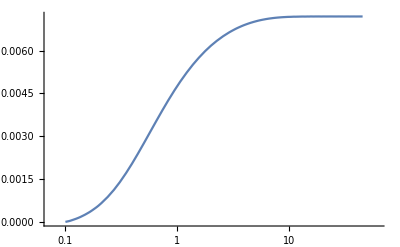

```mathematica
LogLinearPlot[deltaρa[x],{x,0.1,46}]
```

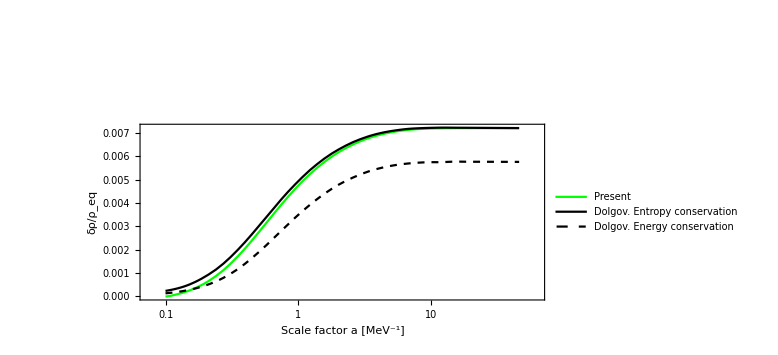

```mathematica
Show[LogLinearPlot[{deltaρa[x],deltaρaDolgovFunc[x],deltaρaDolgovFuncNonconserv[x]},{x,0.1,46},PlotRange->All(*{{0.1,100},{0,0.008}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δρ/ρ_eq"},PlotStyle->{{Thick,Green},{Black},{Dashed,Black}},Epilog->{Text["Standard BBN",{Log[0.2],0.022}]},ImageSize->Large,PlotLegends->{"Present","Dolgov. Entropy conservation","Dolgov. Energy conservation"}]]
```

```mathematica
Export["delta_rho.png",%]
```

delta_rho.png